## Imported Soliton

## 1. Imported soliton with no changes

### UPDATED r0 = 15 kpc (gets converted to code units offset option = 0 (no random radial offsets) Ne = 1 ( number of particles in a ring) nbins = 4 (number of bins for power spectrum) N = 100,000 timesteps dt = 1,000,000 years (gets converted to code units) imported potential = soliton from phi_000000.h5 leapfrog with ChplUltra units

#### Import Coordinates

```mathematica
imp1posxy = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-1/pos-vel.csv",{"Data",1;;100000,6;;7}];
imp1posyz = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-1/pos-vel.csv",{"Data",70000;;100000,7;;8}];
imp1period1 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-1/pos-vel.csv",{"Data",1;;22300,6;;7}];
imp1period2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-1/pos-vel.csv",{"Data",22300;;44600,6;;7}];
imp1period3 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-1/pos-vel.csv",{"Data",44600;;66950,6;;7}];
imp1period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-1/pos-vel.csv",{"Data",66950;;89000,6;;7}];
imp1period5 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-1/pos-vel.csv",{"Data",89500;;100000,6;;7}];
```

#### Comparison

```mathematica
bp9posxy = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv", {"Data", 1 ;;100000, 6 ;; 7}];
bp9posyz = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv", {"Data", 70000 ;; 100000, 7 ;; 8}];
bp9period1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv", {"Data", 1 ;; 22300, 6 ;; 7}];
bp9period2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv", {"Data", 22300 ;; 44600, 6 ;; 7}];
bp9period3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv", {"Data", 44600 ;; 66950, 6 ;; 7}];
bp9period4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv", {"Data", 66950 ;; 89000, 6 ;; 7}];
bp9period5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv", {"Data", 89500 ;; 100000, 6 ;; 7}];
Differences[{bp9posxy, imp1posxy}]
```

{{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},99951,{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}}
 |  |  |  |

#### Position Graph 1

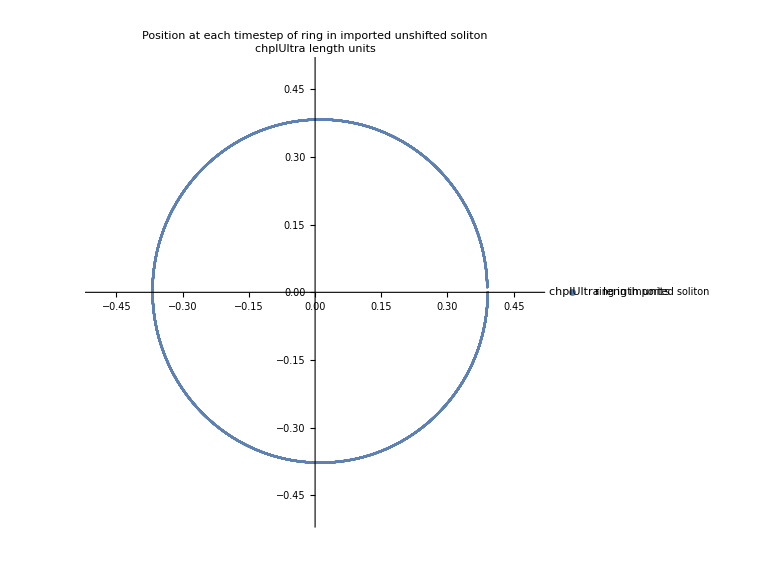

```mathematica
imp1posxygraph = ListPlot[{imp1period1},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"ring in imported soliton "},AxesLabel->{"chplUltra length units","chplUltra length units"}, PlotLabel->"Position at each timestep of ring in imported unshifted soliton"]
```

## 2. Imported soliton with center shifted

### (UPDATED) Assumed indexing scheme 128 gridspaces, represented by 128 points (one endpoint must be missing) -1.0____0.0____1.0 |______| In this case, center should end up right on a gridpoint. Therefore, if there is a center shift at all, it should be by a full gridpoint. However, a full gridpoint shift turns out to be way too much. It doesn’t make logical sense to shift by half a gridpoint with this indexing scheme.s r0 = 15 kpc (gets converted to code units) offset option = 0 (no random radial offsets) Ne = 1 ( number of particles in a ring) nbins = 4 (number of bins for power spectrum) N = 100,000 timesteps dt = 1,000,000 years (gets converted to code units) imported potential = soliton from phi_000000.h5 center offset = (-dr/2, -dr / 2, -dr / 2) (shift in all directions) leapfrog with ChplUltra units

#### Import Coordinates

```mathematica
imp2posxy = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-2/pos-vel.csv",{"Data",1;;100000,6;;7}];
imp2posyz = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-2/pos-vel.csv",{"Data",70000;;100000,7;;8}];
imp2period1 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-2/pos-vel.csv",{"Data",1;;22300,6;;7}];
imp2period2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-2/pos-vel.csv",{"Data",22300;;44600,6;;7}];
imp2period3 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-2/pos-vel.csv",{"Data",44600;;66950,6;;7}];
imp2period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-2/pos-vel.csv",{"Data",66950;;89000,6;;7}];
imp2period5 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-2/pos-vel.csv",{"Data",89500;;100000,6;;7}];
```

#### Comparison

```mathematica
bp12posxy = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",1;;100000,6;;7}];
bp12period1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",1;;22300,6;;7}];
bp12period2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",22300;;44600,6;;7}];
bp12period3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",44600;;66950,6;;7}];
bp12period4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",66950;;89000,6;;7}];
bp12period5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",89500;;100000,6;;7}];
Differences[{imp2posxy,bp12posxy}];
```

#### Position Graph 1

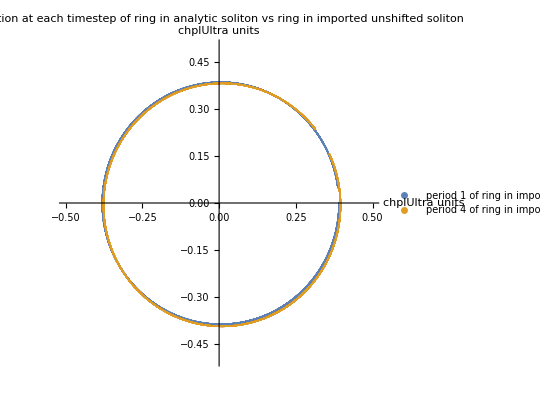

```mathematica
imp2posxygraph = ListPlot[{imp2period1,imp2period4},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Full,PlotLegends->{"period 1 of ring in imported soliton ","period 4 of ring in imported soliton","period 4 of ring in imported unshifted soliton"},AxesLabel->{"chplUltra units","chplUltra units"}, PlotLabel->"Position at each timestep of ring in analytic soliton vs ring in imported unshifted soliton"]
```

## 3. Imported soliton with center shifted

### (UPDATED) Assumed indexing scheme 127 gridspaces, represented by 128 points (both endpoints included -1.0____0.0____1.0 In this case, the center does fall at half a gridpoint, and it does make sense to add a center shift of half a gridpoint (running for 5 times as long it still doesn’t precess!) r0 = 15 kpc (gets converted to code units) offset option = 0 (no random radial offsets) Ne = 1 ( number of particles in a ring) nbins = 4 (number of bins for power spectrum) N = 100,000 timesteps dt = 1,000,000 years (gets converted to code units) imported potential = soliton from phi_000000.h5 center offset = (-dr/2, -dr / 2, -dr / 2) (shift in all directions) leapfrog with ChplUltra units

#### Import Coordinates

```mathematica
imp3posxy = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-3/pos-vel.csv",{"Data",1;;100000,6;;7}];
imp3posyz = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-3/pos-vel.csv",{"Data",70000;;100000,7;;8}];
imp3period1 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-3/pos-vel.csv",{"Data",1;;22300,6;;7}];
imp3period2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-3/pos-vel.csv",{"Data",22300;;44600,6;;7}];
imp3period3 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-3/pos-vel.csv",{"Data",44600;;66950,6;;7}];
imp3period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-3/pos-vel.csv",{"Data",66950;;89000,6;;7}];
imp3period5 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-3/pos-vel.csv",{"Data",89500;;100000,6;;7}];
(*imp3period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-3/pos-vel.csv",{"Data",490000;;500000,6;;7}];*)
```

#### Position Graph 1

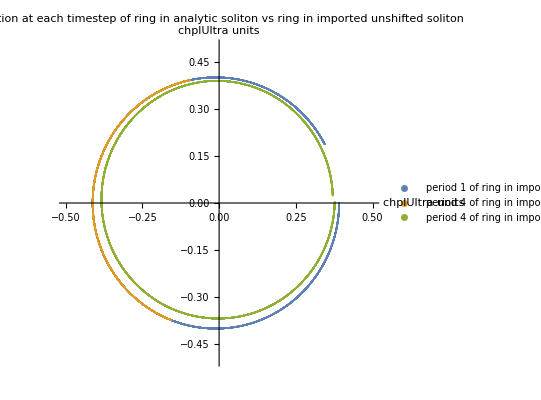

```mathematica
imp3posxygraph = ListPlot[{imp3period1, imp3period4,imp1period4},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Full,PlotLegends->{"period 1 of ring in imported soliton ","period 4 of ring in imported soliton","period 4 of ring in imported unshifted soliton"},AxesLabel->{"chplUltra units","chplUltra units"}, PlotLabel->"Position at each timestep of ring in analytic soliton vs ring in imported unshifted soliton"]
```

## 4. Imported Analytic soliton without center shift

### UPDATED r0 = 15 kpc (gets converted to code units) offset option = 0 (no random radial offsets) Ne = 1 ( number of particles in a ring) nbins = 4 (number of bins for power spectrum) N = 100,000 timesteps dt = 1,000,000 years (gets converted to code units) leapfrog with ChplUltra units po = (0.5**4) * 27492.260803351877 rc = 2.0*0.05359134269304645

#### Import Coordinates

```mathematica
imp4posxy = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-1/pos-vel.csv",{"Data",1;;100000,6;;7}]
imp4posyz = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-1/pos-vel.csv",{"Data",1;;100000,7;;8}];
imp4period1 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-1/pos-vel.csv",{"Data",1;;22300,6;;7}];
imp4period2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-1/pos-vel.csv",{"Data",22300;;44600,6;;7}];
imp4period3 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-1/pos-vel.csv",{"Data",44600;;66950,6;;7}];
imp4period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-1/pos-vel.csv",{"Data",66950;;89000,6;;7}];
imp4period5 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-1/pos-vel.csv",{"Data",89500;;100000,6;;7}];
```

{{0.391023,-9.57731×10^-17},{0.391023,-0.000104858},{0.391023,-0.000209716},{0.391023,-0.000314574},{0.391023,-0.000419432},{0.391023,-0.000524289},{0.391023,-0.000629147},{0.391022,-0.000734005},{0.391022,-0.000838863},{0.391022,-0.00094372},{0.391022,-0.00104858},{0.391021,-0.00115344},99977,{-0.845273,0.0961466},{-0.845273,0.0961952},{-0.845274,0.0962438},{-0.845275,0.0962923},{-0.845276,0.0963409},{-0.845276,0.0963895},{-0.845277,0.0964381},{-0.845278,0.0964867},{-0.845278,0.0965353},{-0.845279,0.0965838},{-0.845279,0.0966324}}
 |  |  |  |

#### Comparison

```mathematica
(*box1 contains CSV box of imported analytic soliton, which contains acceleration at every point, store in a 2D array of 16384 rows with 128 cols each, where each col corresponds to a different z value, and every 128 rows corresponds to a different x value, and every row corresponds to a different y value*)
box1raw = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-1/box-pot.csv",{"Data",1;;16384,1}];
box1 = {};
For[i=1,i<16385,i++,AppendTo[box1,ToExpression[StringSplit[box1raw[[i]]," "]]]]
box1
```

{1}
 |  |  |  |

Plot radius vs acceleration for imported analytic soliton box

```mathematica
imp3acc = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-acc.csv",{"Data",1;;127,1;;2}];
```

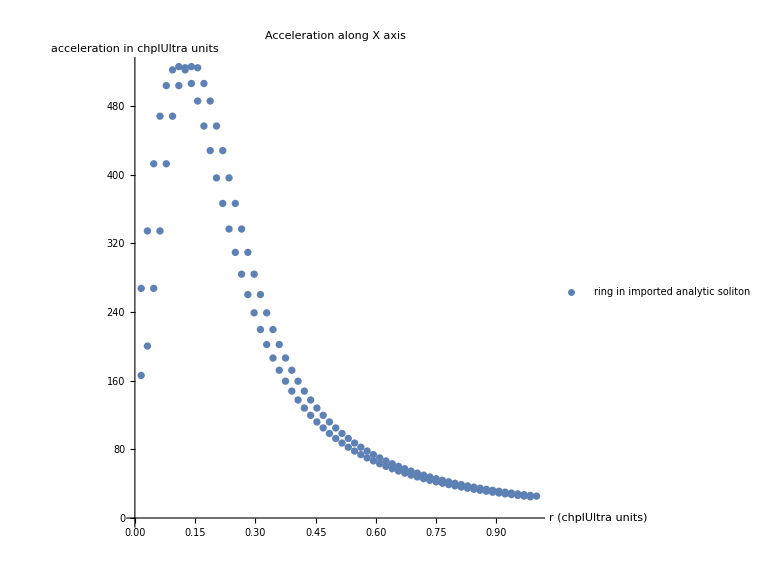

```mathematica
imp3accgraph = ListPlot[{imp3acc},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"ring in imported analytic soliton "},AxesLabel->{"r (chplUltra units)","acceleration in chplUltra units"}, PlotLabel->"Acceleration along X axis"]
```

```mathematica
(*pot consists of a 3D array containing the potential at every point in space.*)
ff = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Code/phi_000000.h5", "Data"];
pot = ff["/phi"]
Dimensions[pot]
```

{{{-14.5467,-14.6231,-14.6994,-14.7757,-14.8519,-14.928,-15.0039,-15.0797,-15.1553,-15.2306,-15.3057,-15.3805,-15.455,-15.529,-15.6027,-15.6759,-15.7487,-15.8209,-15.8925,-15.9636,-16.0339,-16.1036,-16.1726,-16.2408,80,-16.2408,-16.1726,-16.1036,-16.0339,-15.9636,-15.8925,-15.8209,-15.7487,-15.6759,-15.6027,-15.529,-15.455,-15.3805,-15.3057,-15.2306,-15.1553,-15.0797,-15.0039,-14.928,-14.8519,-14.7757,-14.6994,-14.6231,-14.5467},126,{1}},127}
 |  |  |  |

{128,128,128}

I want to compare the csv box created from the analytic soliton to the hdf5 box, but the hdf5 box contains the potential at every point, while the csv box contains the acceleration at every point. I tried to compare both boxes in mathematica but i can only take the gradient of a scalar function, not an arbitrary scalar field. Or I could integrate every point in the csv box to get potential?
I also tried to write a program to compare the two, that calcualtes the gradient of the hdf5 box and compares that to the equivalent value in the csv box. I keep getting seg faults whenever I try to print any value from the Hdf5 box, even if it’s definitely within bounds. I checked if this occurs when I call the main force function from streakline, and it does too. However, this doesn’t occur if I try a previous run where I use the hdf5 box - im able to print values out just fine.  In other words, the same exact location in the array that i access and print out just fine in a previous run, I’m unable to print without a seg fault in this code.

```mathematica
comparison = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/comparison.csv",{"Data",1;;16384,128}]
```

{0.591029,0.503069,0.51061,0.518192,0.525819,0.53348,0.541176,0.548891,0.556631,0.564388,0.572142,0.5799,0.587649,0.59539,0.603105,0.610783,0.61843,0.626029,0.633573,0.641022,0.648423,0.655781,0.663021,0.670062,0.677126,0.683929,0.690688,0.697319,0.703732,16326,0.134293,0.129511,0.12479,0.120112,0.115655,0.111198,0.106916,0.102784,0.0986735,0.0947554,0.090898,0.0871673,0.0834876,0.0799608,0.0765369,0.0732135,0.0700061,0.0668881,0.0638805,0.0609726,0.0581611,0.0554508,0.0528343,0.0503024,0.0478635,0.0455242,0.0432593,0.134019,0.224339}
 |  |  |  |

clearly huge differences....am i taking derivative of potential wrong? shouldn’t it be divided by mass? M = 25 according to config.toml, but not at center, how do i integrate mass

{12.3719,12.5667,12.7645,12.9653,13.1691,13.3759,13.5857,13.7984,14.0139,14.2324,14.4536,14.6775,14.9041,15.1333,15.365,15.5991,15.8355,16.074,16.3146,16.5571,16.8014,17.0472,17.2945,17.5429,17.7923,18.0425,18.2932,18.5442,18.7953,19.046,19.2962,19.5455,19.7936,20.0401,20.2847,20.5271,20.7668,21.0035,21.2367,21.4661,21.6912,21.9115,22.1268,22.3364,22.5401,22.7373,22.9276,23.1105,23.2857,23.4527,23.6112,23.7606,23.9007,24.031,24.1512,24.2611,24.3602,24.4483,24.5252,24.5907,24.6445,24.6865,24.7166,24.7347,24.7407,24.7347,24.7166,24.6865,24.6445,24.5907,24.5252,24.4483,24.3602,24.2611,24.1512,24.031,23.9007,23.7606,23.6112,23.4527,23.2857,23.1105,22.9276,22.7373,22.5401,22.3364,22.1268,21.9115,21.6912,21.4661,21.2367,21.0035,20.7668,20.5271,20.2847,20.0401,19.7936,19.5455,19.2962,19.046,18.7953,18.5442,18.2932,18.0425,17.7923,17.5429,17.2945,17.0472,16.8014,16.5571,16.3146,16.074,15.8355,15.5991,15.365,15.1333,14.9041,14.6775,14.4536,14.2324,14.0139,13.7984,13.5857,13.3759,13.1691,12.9653,12.7645,12.5667}

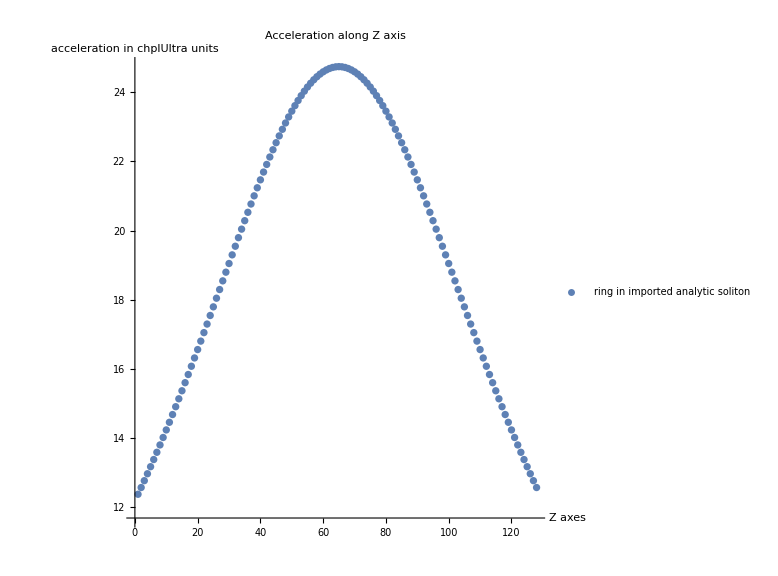

```mathematica
(*graphing a radial slice of acceleration along the z axis of the imported analytic soliton.*) 
zaxis= box1[[8065]]
zaxispotgraph = ListPlot[{zaxis},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"ring in imported analytic soliton "},AxesLabel->{"Z axes","acceleration in chplUltra units"}, PlotLabel->"Acceleration along Z axis"]
```

#### Position Graph 1

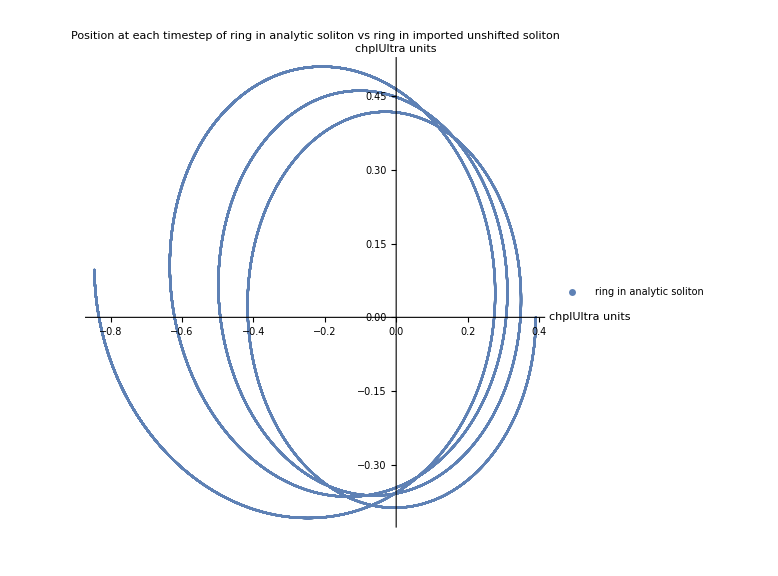

```mathematica
anly4posxygraph = ListPlot[{imp4posxy},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"ring in analytic soliton "},AxesLabel->{"chplUltra units","chplUltra units"}, PlotLabel->"Position at each timestep of ring in analytic soliton vs ring in imported unshifted soliton"]
```

## 5. Imported Analytic soliton with center shift

### r0 = 15 kpc (gets converted to code units offset option = 0 (no random radial offsets) Ne = 1 ( number of particles in a ring) nbins = 4 (number of bins for power spectrum) N = 100,000 timesteps dt = 1,000,000 years (gets converted to code units) leapfrog with ChplUltra units center offset = (-0.0078125,0.00585938,0.0) - imported soliton’s center was shifted right and down to recenter meaning it was originally to the left and up. shift analytic soliton’s center left and up to imitate where imported soliton’s center was originally in creation of analytic soliton. po = (0.5**4) * 27492.260803351877 rc = 2.0*0.05359134269304645

#### Import coordinates

```mathematica
imp5posxy = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-2/pos-vel.csv",{"Data",1;;100000,6;;7}];
imp5posyz = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-2/pos-vel.csv",{"Data",1;;100000,7;;8}];
imp5period1 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-2/pos-vel.csv",{"Data",1;;22300,6;;7}];
imp5period2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-2/pos-vel.csv",{"Data",22300;;44600,6;;7}];
imp5period3 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-2/pos-vel.csv",{"Data",44600;;66950,6;;7}];
imp5period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-2/pos-vel.csv",{"Data",66950;;89000,6;;7}];
imp5period5 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-2/pos-vel.csv",{"Data",89500;;100000,6;;7}];
```

#### Comparison

```mathematica
box2raw = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-imp-csvbox-2/box-pot.csv",{"Data",1;;16384,1}];
box2 = {};
For[i=1,i<16385,i++,AppendTo[box2,ToExpression[StringSplit[box2raw[[i]]," "]]]]
```

#### Position Graph 1

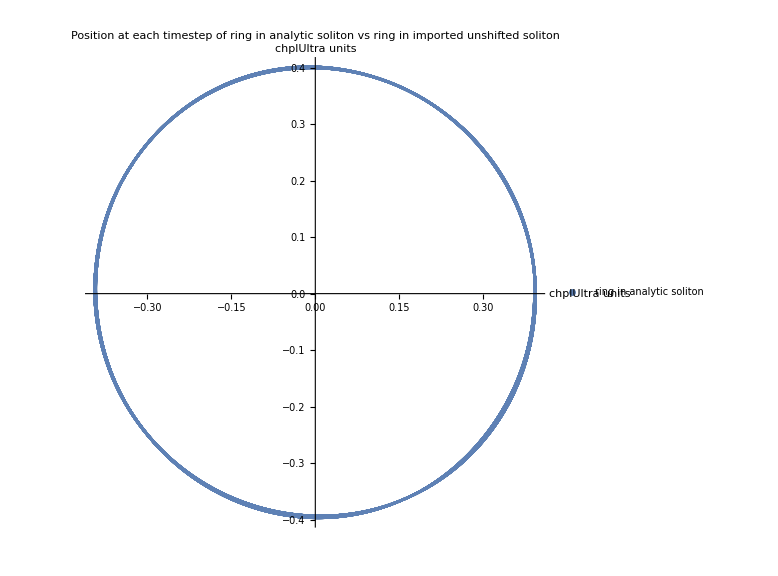

```mathematica
imp5posxygraph = ListPlot[{imp5posxy},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"ring in analytic soliton "},AxesLabel->{"chplUltra units","chplUltra units"}, PlotLabel->"Position at each timestep of ring in analytic soliton vs ring in imported unshifted soliton"]
```

## Analytic Soliton

## 1. Analytic soliton with no changes

### r0 = 15 kpc (gets converted to code units offset option = 0 (no random radial offsets) Ne = 1 ( number of particles in a ring) nbins = 4 (number of bins for power spectrum) N = 100,000 timesteps dt = 1,000,000 years (gets converted to code units) leapfrog with ChplUltra units po = (0.5**4) * 27492.260803351877 rc = 2.0*0.05359134269304645

#### Import coordinates

```mathematica
anly1posxy = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-1/pos-vel.csv",{"Data",1;;100000,6;;7}]
anly1posyz = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-1/pos-vel.csv",{"Data",1;;100000,7;;8}];
anly1period1 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-1/pos-vel.csv",{"Data",1;;22300,6;;7}];
anly1period2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-1/pos-vel.csv",{"Data",22300;;44600,6;;7}];
anly1period3 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-1/pos-vel.csv",{"Data",44600;;66950,6;;7}];
anly1period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-1/pos-vel.csv",{"Data",66950;;89000,6;;7}];
anly1period5 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-1/pos-vel.csv",{"Data",89500;;100000,6;;7}];
```

{{0.391023,-9.57731×10^-17},{0.391023,-0.000104764},{0.391023,-0.000209527},{0.391023,-0.000314291},{0.391023,-0.000419055},{0.391023,-0.000523818},{0.391023,-0.000628582},{0.391022,-0.000733345},{0.391022,-0.000838109},{0.391022,-0.000942872},99981,{-0.0336792,-0.38957},{-0.0337836,-0.389561},{-0.033888,-0.389552},{-0.0339923,-0.389543},{-0.0340967,-0.389534},{-0.0342011,-0.389525},{-0.0343054,-0.389515},{-0.0344098,-0.389506},{-0.0345141,-0.389497}}
 |  |  |  |

#### Comparison

```mathematica
bp8posxy = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp15.csv",{"Data",1;;100000,6;;7}];
bp8period1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp15.csv",{"Data",1;;22300,6;;7}];
Differences[{bp8posxy,anly1posxy}]
```

{{{0.,0.},{0.,-5.98×10^-7},{0.,-1.195×10^-6},{0.,-1.793×10^-6},{0.,-2.391×10^-6},{0.,-2.988×10^-6},{0.,-3.586×10^-6},99986,{-0.0597025,0.000618},{-0.0597029,0.000634},{-0.0597034,0.00065},{-0.0597038,0.000666},{-0.0597042,0.000682},{-0.0597046,0.000698},{-0.059705,0.000714}}}
 |  |  |  |

```mathematica
anly1posxy
```

{{0.391023,-9.57731×10^-17},{0.391023,-0.000104166},{0.391023,-0.000208332},{0.391023,-0.000312498},{0.391023,-0.000416664},{0.391023,-0.00052083},{0.391023,-0.000624996},{0.391022,-0.000729161},{0.391022,-0.000833327},{0.391022,-0.000937493},99981,{0.0260224,-0.390156},{0.0259185,-0.390163},{0.0258145,-0.39017},{0.0257106,-0.390177},{0.0256067,-0.390184},{0.0255027,-0.390191},{0.0253988,-0.390197},{0.0252948,-0.390204},{0.0251909,-0.390211}}
 |  |  |  |

#### Position Graph 1

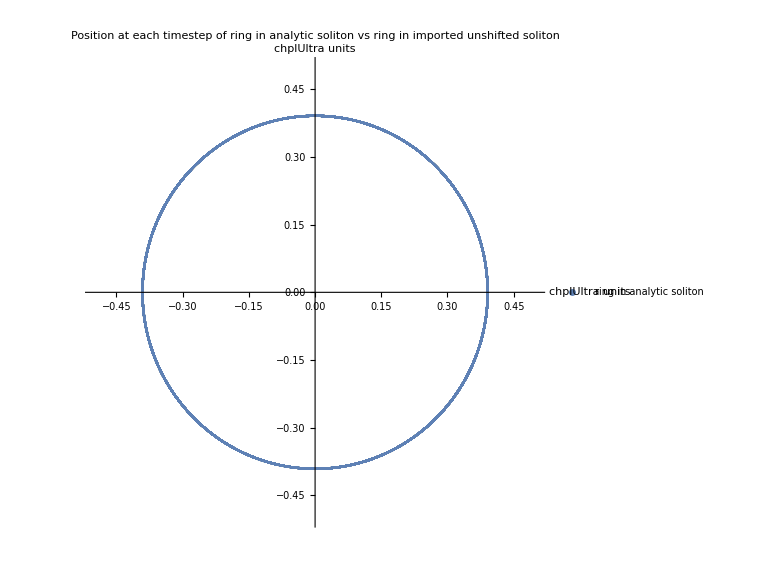

```mathematica
anly1posxygraph = ListPlot[{anly1posxy},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"ring in analytic soliton "},AxesLabel->{"chplUltra units","chplUltra units"}, PlotLabel->"Position at each timestep of ring in analytic soliton vs ring in imported unshifted soliton"]
```

### 2.

## 2. Analytic soliton with center shifted

### r0 = 15 kpc (gets converted to code units offset option = 0 (no random radial offsets) Ne = 1 ( number of particles in a ring) nbins = 4 (number of bins for power spectrum) N = 100,000 timesteps dt = 1,000,000 years (gets converted to code units) potential = soliton equation po = (0.5**4) * 27492.260803351877 rc = 2.0*0.05359134269304645 leapfrog with ChplUltra units center offset = (-0.0078125,0.00585938,0.0) - imported soliton’s center was shifted right and down; shift analytic soliton’s center left and up to imitate where imported soliton’s center was originally

#### Import Coordinates

```mathematica
anly2posxy = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-2/pos-vel.csv",{"Data",1;;100000,6;;7}];
anly2posyz = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-2/pos-vel.csv",{"Data",1;;100000,7;;8}];
anly2period1 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-2/pos-vel.csv",{"Data",1;;22300,6;;7}];
anly2period2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-2/pos-vel.csv",{"Data",22300;;44600,6;;7}];
anly2period3 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-2/pos-vel.csv",{"Data",44600;;66950,6;;7}];
anly2period4 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-2/pos-vel.csv",{"Data",66950;;89000,6;;7}];
anly2period5 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/soliton-anly-2/pos-vel.csv",{"Data",89500;;100000,6;;7}];
```

#### Comparison

```mathematica
Differences[{anly2posxy,imp1posxy}]
```

{{{0.,0.},{0.,3.797×10^-6},{0.,7.594×10^-6},{0.,0.00001139},{0.,0.000015188},{0.,0.000018987},{0.,0.000022785},{0.,0.000026585},{0.,0.000030385},{0.,0.000034185},99981,{-0.92604,-0.231214},{-0.926027,-0.231025},{-0.926014,-0.230836},{-0.926002,-0.230647},{-0.925989,-0.230458},{-0.925975,-0.230269},{-0.925963,-0.23008},{-0.92595,-0.229891},{-0.925937,-0.229702}}}
 |  |  |  |

#### Position Graph 1

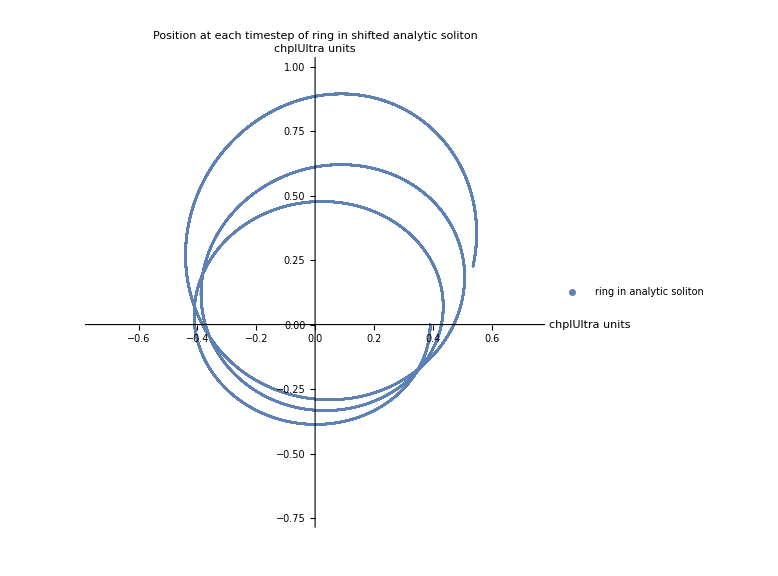

```mathematica
anly2posxygraph = ListPlot[{anly2posxy},PlotRange->{{-0.75,0.75},{-0.75,1.0}},AspectRatio->1,ImageSize->Large,PlotLegends->{"ring in analytic soliton "},AxesLabel->{"chplUltra units","chplUltra units"}, PlotLabel->"Position at each timestep of ring in shifted analytic soliton"]
```

## Box Comparison

## 1. Unshifted imported ChplUltra soliton vs unshifted analytic soliton

Compare the analytic soliton approximation, mapped to a grid and imported into a csv box, to the HDF5 potential.

### Acceleration magnitudes along z = 0 plane

```mathematica
comp1anlyacc = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-acc1.csv",{"Data",1;;127,1;;2}];
comp1hdf5acc = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-acc1.csv",{"Data",1;;127,3;;4}];
```

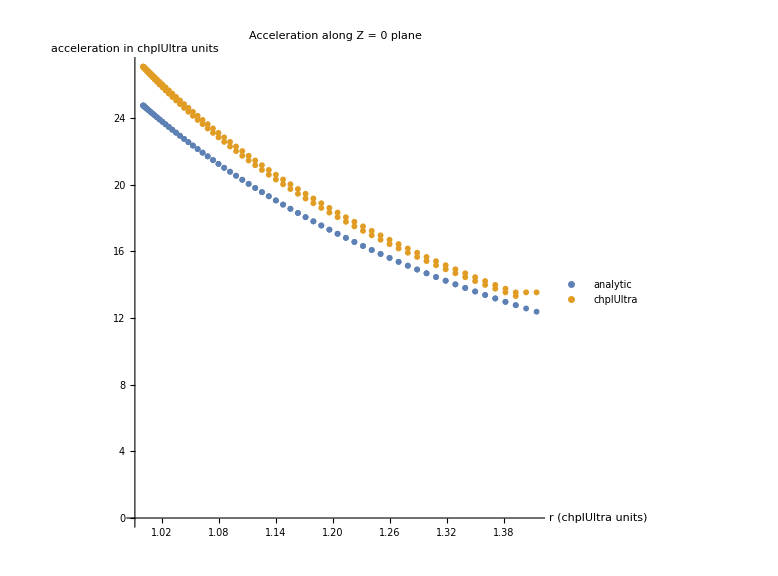

```mathematica
comp1accgraph = ListPlot[{comp1anlyacc,comp1hdf5acc},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","acceleration in chplUltra units"}, PlotLabel->"Acceleration along Z = 0 plane"]
```

Set::write: Tag Times in … is Protected.

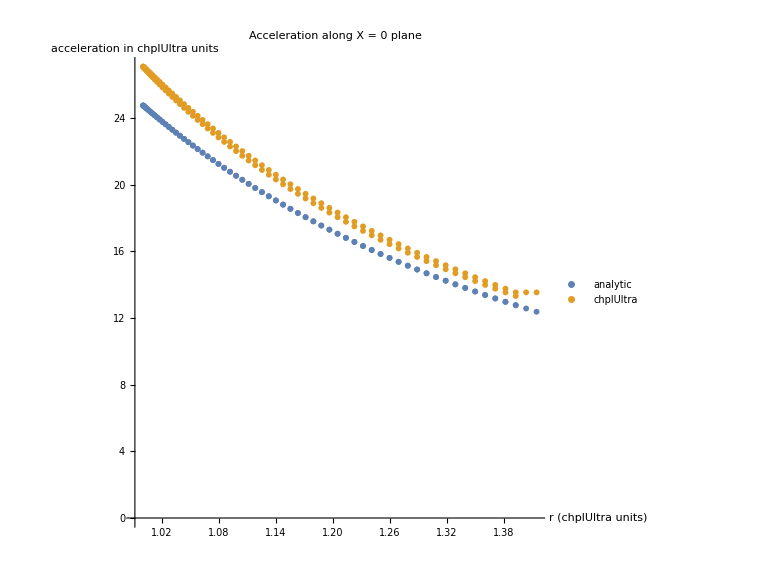

```mathematica
comp1anlyacc2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-acc2.csv",{"Data",1;;127,1;;2}];
comp1hdf5acc2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-acc2.csv",{"Data",1;;127,3;;4}];
comp1accgraph 2= ListPlot[{comp1anlyacc2,comp1hdf5acc2},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","acceleration in chplUltra units"}, PlotLabel->"Acceleration along X = 0 plane"]
```

### Mass

```mathematica
comp1anlymass = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-mass.csv",{"Data",1;;1072,1;;2}];
comp1hdf5mass = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-mass2.csv",{"Data",1;;860370,1;;2}];
```

```mathematica
comp1massgraph = ListPlot[{comp1anlymass,comp1hdf5mass},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","mass (ChplUltra units)"}, PlotLabel->"Mass"]
```

-Graphics-

### Potentials

```mathematica
comp1anlypot = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-pot.csv",{"Data",1;;1072,1;;2}];
comp1hdf5pot = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-1/plot-pot2.csv",{"Data",1;;860370,1;;2}];
```

```mathematica
comp1potgraph = ListPlot[{comp1anlypot,comp1hdf5pot},PlotRange->{{0,2.0},{-140,0}},AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","Potential (ChplUltra units)"}, PlotLabel->"Potential"]
```

-Graphics-

## 2. Shifted imported ChplUltra soliton vs unshifted analytic soliton

#### Acceleration magnitudes along z = 0 plane

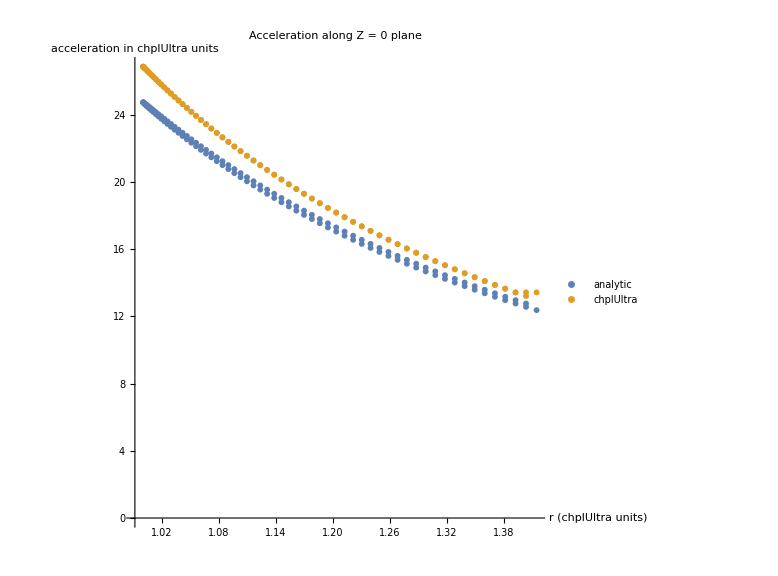

```mathematica
comp2anlyacc = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-2/plot-acc1.csv",{"Data",1;;127,1;;2}];
comp2hdf5acc = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-2/plot-acc1.csv",{"Data",1;;127,3;;4}];
comp2accgraph = ListPlot[{comp2anlyacc,comp2hdf5acc},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","acceleration in chplUltra units"}, PlotLabel->"Acceleration along Z = 0 plane"]
```

```mathematica
ListPlot[{{{}},{{}}},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","acceleration in chplUltra units"},PlotLabel->"Acceleration along Z = 0 plane"]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{{{}},{{}}},PlotRange→Automatic,AspectRatio→1,ImageSize→Large,PlotLegends→{analytic,chplUltra},AxesLabel→{r (chplUltra units),acceleration in chplUltra units},PlotLabel→Acceleration along Z = 0 plane]

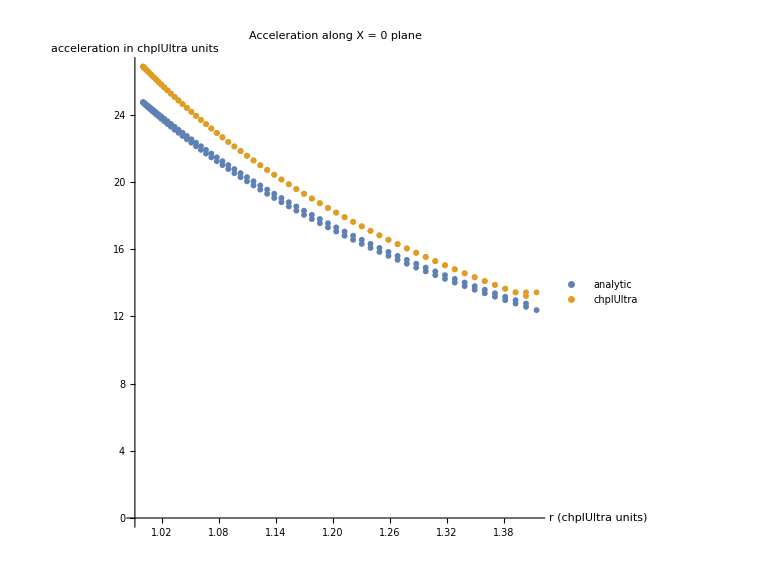

```mathematica
comp2anlyacc2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-2/plot-acc2.csv",{"Data",1;;127,1;;2}];
comp2hdf5acc2 = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-2/plot-acc2.csv",{"Data",1;;127,3;;4}];
comp2accgraph2 = ListPlot[{comp2anlyacc2,comp2hdf5acc2},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","acceleration in chplUltra units"}, PlotLabel->"Acceleration along X = 0 plane"]
```

### Mass

```mathematica
comp2anlymass = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-2/plot-mass.csv",{"Data",1;;1072,1;;2}];
comp2hdf5mass = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-2/plot-mass2.csv",{"Data",1;;860370,1;;2}];
comp2massgraph = ListPlot[{comp2anlymass,comp2hdf5mass},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","mass (ChplUltra units)"}, PlotLabel->"Mass"]
```

-Graphics-

### Potentials

```mathematica
comp2anlypot = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-2/plot-pot.csv",{"Data",1;;1072,1;;2}];
comp2hdf5pot = Import["/Users/clairerecamier/Desktop/Github/StellarStreams/Runs/Soliton/potbox-comp-2/plot-pot2.csv",{"Data",1;;860370,1;;2}];
comp2potgraph = ListPlot[{comp2anlypot,comp2hdf5pot},PlotRange->{{0,2.0},{-140,0}},AspectRatio->1,ImageSize->Large,PlotLegends->{"analytic","chplUltra"},AxesLabel->{"r (chplUltra units)","Potential (ChplUltra units)"}, PlotLabel->"Potential"]
```

-Graphics-